```mathematica
sortCC[polyinds_]:=Block[{cent,poly},
poly=Lookup[indToPtsAssoc,polyinds];
Lookup[ptsToIndAssoc,
DeleteDuplicates@Flatten[MeshPrimitives[ConvexHullMesh[poly],1]/.Line->Sequence,1]
]
];

Clear[sortPointsCC];
sortPointsCC[polyinds_,indTopts_,ptsToInds_]:=Block[{cent,ordering,polyPoints},
polyPoints=Lookup[indTopts,polyinds];
cent=Mean@polyPoints;
ordering=Ordering[ArcTan[#[[1]],#[[2]]]&@(#-cent)&/@polyPoints];Lookup[ptsToInds,Part[polyPoints,ordering]]
]
```

```mathematica
Clear@T1transitionFn;
T1transitionFn[findEdges_,indToPtsAssoc_,vertexToCellG_,cellToVertexG_,dSep_:0.02]:=Block[{edgeind,connectedcellKeys,edge,newpts,cellvertIndices,cellvertices,pos,cellpolys,memF,keyscellP,selcellKeys,ptToCell,newptsindices,indToPts=indToPtsAssoc,ptsToInds,
PtIndToCell,keysToMap,cellindicesAssoc,f1,otherkeys,f2,polysharingEdge,bag=CreateDataStructure["DynamicArray"],vertToCellG=vertexToCellG,cellToVertG=cellToVertexG,testpts},
If[findEdges≠{},
Scan[
(edgeind=#;
If[ContainsAll[Keys[indToPts],edgeind],
(* should be an edge not connected to an edge that has already undergone a T1 *)
connectedcellKeys=DeleteDuplicates[Flatten@Lookup[vertToCellG,edgeind]];
cellvertIndices=Lookup[cellToVertG,connectedcellKeys];
edge=Lookup[indToPts,edgeind];
If[Length[connectedcellKeys]==1,
(*edge that is exposed to the void to be merged as a single vertex*)
newpts=Mean[edge];
newptsindices=Max[Keys@indToPts]+1;
KeyDropFrom[indToPts,edgeind];
AppendTo[indToPts,newptsindices->newpts];
bag["Append",edgeind];
ptsToInds=AssociationMap[Reverse,indToPts];
cellToVertG=MapAt[
DeleteDuplicates[#/.(Alternatives@@edgeind)-> newptsindices]&,
cellToVertG,Key[connectedcellKeys/.{z_Integer}:>z]
],
(*else proceed with T1 transition*)
newpts=With[{midPt=Mean[edge]},
midPt+dSep Normalize[(#-midPt)]&/@Flatten[RotationTransform[-π/2,midPt]/@{edge},1]
];
testpts=With[{midPt=Mean[edge]},
midPt+0.000001Normalize[(#-midPt)]&/@newpts
];
pos=Position[cellvertIndices,{OrderlessPatternSequence[___,First@edgeind,___,Last@edgeind,___]},{1}];
polysharingEdge=Extract[cellvertIndices,pos];
(* the edge should not be part of any Δ *)
If[(AllTrue[polysharingEdge,Length[#]≠3&])&&ContainsNone[edgeind,Union@*Flatten@*Normal@bag],
cellvertices=Map[Lookup[indToPts,#]&,cellvertIndices];
cellpolys=Polygon/@cellvertices;
memF=Function[x,RegionMember@x,Listable][Extract[cellpolys,pos]];
keyscellP=Extract[connectedcellKeys,pos];
selcellKeys=Thread[keyscellP->memF];
ptToCell=Quiet[#->First@@Select[selcellKeys,Function[x,Last[x][#]]]&/@testpts/.HoldPattern[_->First[]]->Nothing] ;(* pt to cell *)
ptToCell=ptToCell/.Thread[testpts->newpts];
newptsindices=Range[#+1,#+2]&[Max[Keys@indToPts]];
KeyDropFrom[indToPts,edgeind];
AppendTo[indToPts,Thread[newptsindices->newpts]];
ptsToInds=AssociationMap[Reverse,indToPts];
bag["Append",edgeind];
PtIndToCell=MapAt[ptsToInds,ptToCell,{All,1}]/.Rule->List ;(*index to cell*)
keysToMap=MapAt[Key,PtIndToCell,{All,2}];
cellindicesAssoc=AssociationThread[connectedcellKeys,cellvertIndices];

f1=Fold[MapAt[Function[x,DeleteDuplicates[x/.Thread[ edgeind->#2[[1]] ]]],#1,#2[[2]]]&,cellindicesAssoc,keysToMap];
otherkeys=List@*Key/@Complement[connectedcellKeys,keyscellP];
f2=MapAt[(#/.(Alternatives@@edgeind)->Splice[newptsindices]//sortPointsCC[#,indToPts,ptsToInds]&)&,f1,otherkeys];
AppendTo[cellToVertG,f2];
];
];
vertToCellG=GroupBy[Flatten[(Reverse[#,2]&)@*Thread/@Normal@cellToVertG],First->Last];
])&,findEdges]
];
{indToPts,cellToVertG,vertToCellG}
];
```

## T1 transition

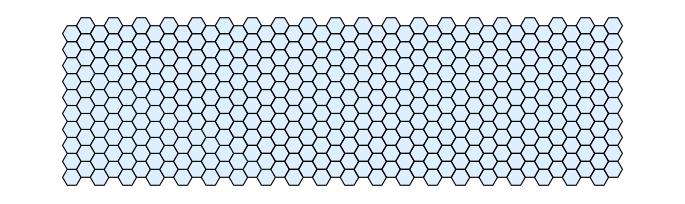

```mathematica
hexTile[n_,m_]:=With[{hex=Polygon[Table[{Cos[2 Pi k/6]+#,Sin[2 Pi k/6]+#2},{k,6}]]&},Table[hex[3 i+3 ((-1)^j+1)/4,Sqrt[3]/2 j],{i,n},{j,m}]];
Graphics[{EdgeForm[Black],LightBlue,hexTile[20,20]}]
```

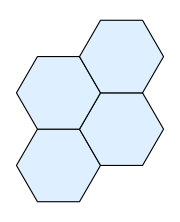

```mathematica
plt=First[hexTile[1,4]]//Map[{EdgeForm[Black],LightBlue,#}&,#]&//Graphics[#,ImageSize->Small]&
```

```mathematica
mesh=First[hexTile[1,4]];
```

```mathematica
cells=(MeshPrimitives[#,0])&/@mesh/.Point->Sequence
```

{{{2.,0.866025},{2.5,0.},{3.5,0.},{4.,0.866025},{3.5,1.73205},{2.5,1.73205}},{{3.5,1.73205},{4.,0.866025},{5.,0.866025},{5.5,1.73205},{5.,2.59808},{4.,2.59808}},{{2.,2.59808},{2.5,1.73205},{3.5,1.73205},{4.,2.59808},{3.5,3.4641},{2.5,3.4641}},{{3.5,3.4641},{4.,2.59808},{5.,2.59808},{5.5,3.4641},{5.,4.33013},{4.,4.33013}}}

```mathematica
ptsToIndAssoc=AssociationThread[#-> Range[Length@#]]&@DeleteDuplicates@Flatten[cells,1]
```

<|{2.,0.866025}→1,{2.5,0.}→2,{3.5,0.}→3,{4.,0.866025}→4,{3.5,1.73205}→5,{2.5,1.73205}→6,{5.,0.866025}→7,{5.5,1.73205}→8,{5.,2.59808}→9,{4.,2.59808}→10,{2.,2.59808}→11,{3.5,3.4641}→12,{2.5,3.4641}→13,{5.5,3.4641}→14,{5.,4.33013}→15,{4.,4.33013}→16|>

```mathematica
indToPtsAssoc=AssociationMap[Reverse,ptsToIndAssoc]
```

<|1→{2.,0.866025},2→{2.5,0.},3→{3.5,0.},4→{4.,0.866025},5→{3.5,1.73205},6→{2.5,1.73205},7→{5.,0.866025},8→{5.5,1.73205},9→{5.,2.59808},10→{4.,2.59808},11→{2.,2.59808},12→{3.5,3.4641},13→{2.5,3.4641},14→{5.5,3.4641},15→{5.,4.33013},16→{4.,4.33013}|>

```mathematica
cellToVertex=AssociationThread[Range@Length@#-> #]&@(Lookup[ptsToIndAssoc,#]&/@cells)
```

<|1→{1,2,3,4,5,6},2→{5,4,7,8,9,10},3→{11,6,5,10,12,13},4→{12,10,9,14,15,16}|>

```mathematica
vertexToCell=GroupBy[Flatten[(Reverse[#,2]&)@*Thread/@Normal@cellToVertex],First-> Last]
```

<|1→{1},2→{1},3→{1},4→{1,2},5→{1,2,3},6→{1,3},7→{2},8→{2},9→{2,4},10→{2,3,4},11→{3},12→{3,4},13→{3},14→{4},15→{4},16→{4}|>

### Case 1

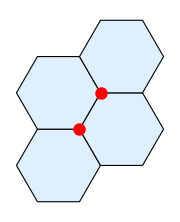

```mathematica
Show[plt,Graphics[{Red,PointSize[0.05],Point@indToPtsAssoc[#]&/@{5,10}}],ImageSize->Small]
```

```mathematica
{$indToPts,$cellToVertex,$vertexToCell}=T1transitionFn[{{5,10}},indToPtsAssoc,vertexToCell,cellToVertex,0.05]
```

{<|1→{2.,0.866025},2→{2.5,0.},3→{3.5,0.},4→{4.,0.866025},6→{2.5,1.73205},7→{5.,0.866025},8→{5.5,1.73205},9→{5.,2.59808},11→{2.,2.59808},12→{3.5,3.4641},13→{2.5,3.4641},14→{5.5,3.4641},15→{5.,4.33013},16→{4.,4.33013},17→{3.7067,2.19006},18→{3.7933,2.14006}|>,<|1→{1,2,3,4,18,17,6},2→{18,4,7,8,9},3→{11,6,17,12,13},4→{17,18,9,14,15,16,12}|>,<|1→{1},2→{1},3→{1},4→{1,2},18→{1,2,4},17→{1,3,4},6→{1,3},7→{2},8→{2},9→{2,4},11→{3},12→{3,4},13→{3},14→{4},15→{4},16→{4}|>}

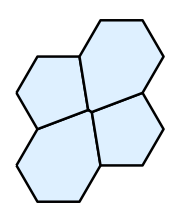

```mathematica
Polygon/@Map[Lookup[$indToPts,#]&,$cellToVertex,{2}]//Values//Graphics[{EdgeForm[{Thickness[0.01],Black}],FaceForm[LightBlue],#},ImageSize->Small]&
```

### Case 2

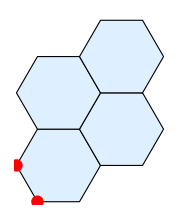

```mathematica
Show[plt,Graphics[{Red,PointSize[0.05],Point@indToPtsAssoc[#]&/@{1,2}}],ImageSize->Small]
```

```mathematica
{$indToPts,$cellToVertex,$vertexToCell}=T1transitionFn[{{1,2}},indToPtsAssoc,vertexToCell,cellToVertex,0.05]
```

{<|3→{3.5,0.},4→{4.,0.866025},5→{3.5,1.73205},6→{2.5,1.73205},7→{5.,0.866025},8→{5.5,1.73205},9→{5.,2.59808},10→{4.,2.59808},11→{2.,2.59808},12→{3.5,3.4641},13→{2.5,3.4641},14→{5.5,3.4641},15→{5.,4.33013},16→{4.,4.33013},17→{2.25,0.433013}|>,<|1→{17,3,4,5,6},2→{5,4,7,8,9,10},3→{11,6,5,10,12,13},4→{12,10,9,14,15,16}|>,<|17→{1},3→{1},4→{1,2},5→{1,2,3},6→{1,3},7→{2},8→{2},9→{2,4},10→{2,3,4},11→{3},12→{3,4},13→{3},14→{4},15→{4},16→{4}|>}

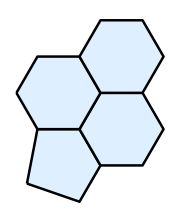

```mathematica
Polygon/@Map[Lookup[$indToPts,#]&,$cellToVertex,{2}]//Values//Graphics[{EdgeForm[{Thickness[0.01],Black}],FaceForm[LightBlue],#},ImageSize->Small]&
```

### Case 3

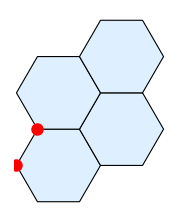

```mathematica
Show[plt,Graphics[{Red,PointSize[0.05],Point@indToPtsAssoc[#]&/@{1,6}}],ImageSize->Small]
```

```mathematica
{$indToPts,$cellToVertex,$vertexToCell}=T1transitionFn[{{1,6}},indToPtsAssoc,vertexToCell,cellToVertex,0.07]
```

{<|2→{2.5,0.},3→{3.5,0.},4→{4.,0.866025},5→{3.5,1.73205},7→{5.,0.866025},8→{5.5,1.73205},9→{5.,2.59808},10→{4.,2.59808},11→{2.,2.59808},12→{3.5,3.4641},13→{2.5,3.4641},14→{5.5,3.4641},15→{5.,4.33013},16→{4.,4.33013},17→{2.18938,1.33404},18→{2.31062,1.26404}|>,<|2→{5,4,7,8,9,10},4→{12,10,9,14,15,16},1→{18,2,3,4,5},3→{17,18,5,10,12,13,11}|>,<|5→{2,1,3},4→{2,1},7→{2},8→{2},9→{2,4},10→{2,4,3},12→{4,3},14→{4},15→{4},16→{4},18→{1,3},2→{1},3→{1},17→{3},13→{3},11→{3}|>}

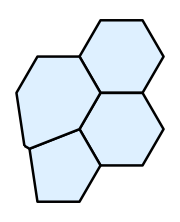

```mathematica
Polygon/@Map[Lookup[$indToPts,#]&,$cellToVertex,{2}]//Values//Graphics[{EdgeForm[{Thickness[0.01],Black}],FaceForm[LightBlue],#},ImageSize->Small]&
```

### Case 4

```mathematica
plt2=-Graphics-;
```

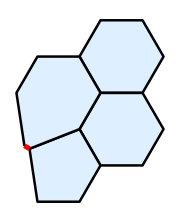

```mathematica
Show[plt2,Graphics[{Red,Thickness[0.02],Line[$indToPts[#]&/@{17,18}]}],ImageSize->Small]
```

```mathematica
{$$indToPts,$$cellToVertex,$$vertexToCell}=T1transitionFn[{{17,18}},$indToPts,$vertexToCell,$cellToVertex,0.1]
```

{<|2→{2.5,0.},3→{3.5,0.},4→{4.,0.866025},5→{3.5,1.73205},7→{5.,0.866025},8→{5.5,1.73205},9→{5.,2.59808},10→{4.,2.59808},11→{2.,2.59808},12→{3.5,3.4641},13→{2.5,3.4641},14→{5.5,3.4641},15→{5.,4.33013},16→{4.,4.33013},19→{2.3,1.38564},20→{2.2,1.21244}|>,<|2→{5,4,7,8,9,10},4→{12,10,9,14,15,16},3→{19,5,10,12,13,11},1→{2,3,4,5,19,20}|>,<|5→{2,3,1},4→{2,1},7→{2},8→{2},9→{2,4},10→{2,4,3},12→{4,3},14→{4},15→{4},16→{4},19→{3,1},13→{3},11→{3},2→{1},3→{1},20→{1}|>}

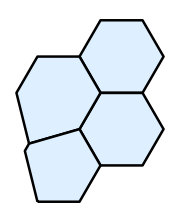

```mathematica
Polygon/@Map[Lookup[$$indToPts,#]&,$$cellToVertex,{2}]//Values//Graphics[{EdgeForm[{Thickness[0.01],Black}],FaceForm[LightBlue],#},ImageSize->Small]&
```

### Case 5

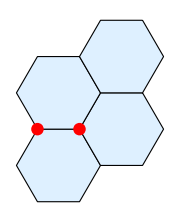

```mathematica
Show[plt,Graphics[{Red,PointSize[0.05],Point@indToPtsAssoc[#]&/@{5,6}}],ImageSize->Small]
```

```mathematica
{$indToPts,$cellToVertex,$vertexToCell}=T1transitionFn[{{5,6}},indToPtsAssoc,vertexToCell,cellToVertex,0.07]
```

{<|1→{2.,0.866025},2→{2.5,0.},3→{3.5,0.},4→{4.,0.866025},7→{5.,0.866025},8→{5.5,1.73205},9→{5.,2.59808},10→{4.,2.59808},11→{2.,2.59808},12→{3.5,3.4641},13→{2.5,3.4641},14→{5.5,3.4641},15→{5.,4.33013},16→{4.,4.33013},17→{3.,1.66205},18→{3.,1.80205}|>,<|4→{12,10,9,14,15,16},1→{1,2,3,4,17},2→{17,4,7,8,9,10,18},3→{11,18,10,12,13}|>,<|12→{4,3},10→{4,2,3},9→{4,2},14→{4},15→{4},16→{4},1→{1},2→{1},3→{1},4→{1,2},17→{1,2},7→{2},8→{2},18→{2,3},11→{3},13→{3}|>}

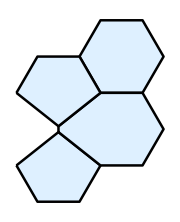

```mathematica
Polygon/@Map[Lookup[$indToPts,#]&,$cellToVertex,{2}]//Values//Graphics[{EdgeForm[{Thickness[0.01],Black}],FaceForm[LightBlue],#},ImageSize->Small]&
```